```mathematica
U[T_,λ4_,λ6_]:=((T-1)/(2))ϕ^2+(λ4/(4!))ϕ^6+(λ6/(6!))ϕ^6
```

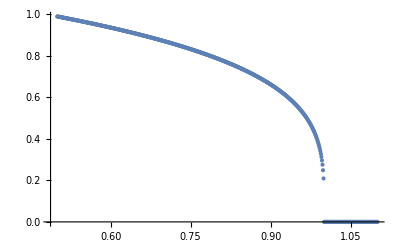

```mathematica
ListPlot[ParallelTable[{T,Abs[ϕ]/.NMinimize[U[T,2,3],ϕ][[2]]},{T,0.5,1.1,0.001}]]
```

```mathematica
U[T_,T0_,a_,λ4_,λ6_,ϕ_]:=a/2(T-T0)ϕ^2+λ4/(4!)ϕ^4+λ6/(6!)ϕ^6;
Ucrit[a_,λ4_,λ6_,ϕ_]:=a/2 Abs[λ4]^2/(8λ6)ϕ^2+λ4/(4!)ϕ^4+λ6/(6!)ϕ^6;
```

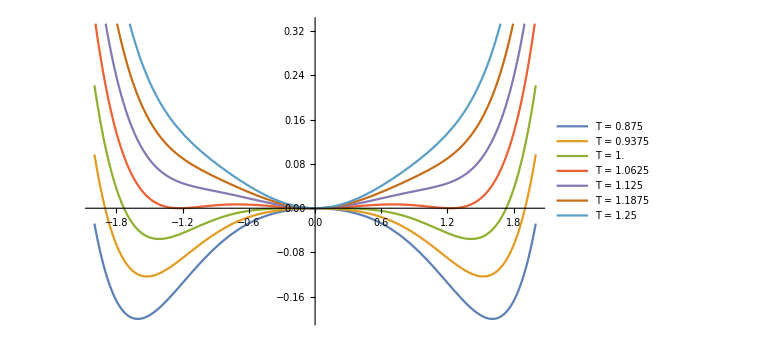

```mathematica
λ4=-10;
λ6=λ4^2;
t0 = 1;
tc = 1.0625;
tmin=0.875;
tmax=1.25;
tstep=1/16;
plots=Table[U[t,t0,1,-1,10,ϕ],{t,tmin,tmax,tstep}];
ts=Table["T = "<>ToString[t],{t,tmin,tmax,tstep}];
Plot[plots,{ϕ,-2,2},PlotLegends->ts,ImageSize->Large]
```

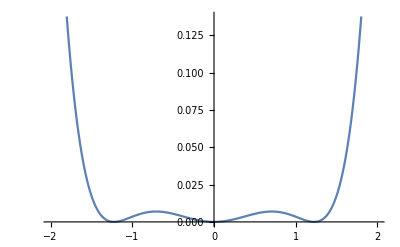

```mathematica
Plot[U[1.0625,t0,1,-1,10,ϕ],{ϕ,-2,2}]
```

```mathematica
Solve[U[(1.06250),t0,1,-1,10,ϕ]==0]
```

{{ϕ→-1.22474},{ϕ→-1.22474},{ϕ→0.},{ϕ→0.},{ϕ→1.22474},{ϕ→1.22474}}

```mathematica
(1.0625-1.0)^-1
```

16.